Create spheroid and plane, plane angle and z position can be varied via control sliders.

```mathematica
h[x_,y_,z_]:=x^2/2+y^2/2+z^2/8;
g[g1_, z1_, x_,y_,z_] := Sqrt[1-z1^2]*y + z1*(z-g1)
Manipulate[ContourPlot3D[{h[x,y,z]==1,g[g1, z1, x, y, z]==0},{x,-4,4},{y,-4,4},{z,-4,4},MeshStyle->{{Thick,Blue}},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]]],{g1, -4, 4}, {z1, 0, 1}]
```

EmptyRegion::pmdim: The embedding dimension 3. should be a machine-sized positive integer.

General::stop: Further output of EmptyRegion :: pmdim will be suppressed during this calculation.

EmptyRegion::pmdim: The embedding dimension 3. should be a machine-sized positive integer.

Get intersection of two geometric objects using Mathematica’s implicit regions.

```mathematica
h[x_, y_, z_]=x^2+y^2+z^2/4;
g[y_, z_, z1_, g1_] = Sqrt[1-z1^2]*y + 0.5*(z-g1);
Manipulate[
reg1=ImplicitRegion[h[x, y,z]==1 && z>1,{x,y,z}];
reg2=ImplicitRegion[g[y, z, i, 1] ==0,{x,y,z}];
reg=RegionIntersection[reg1,reg2];
a=DiscretizeRegion[reg,{{-4,4},{-4,4},{-4,4}}],{i,0, 1} ]
```

DiscretizeRegion::drcd: Available methods not able to resolve all components of dimension 1; these may be omitted from the result.

DiscretizeRegion::dre: DiscretizeRegion did not find any sample points in the region RegionIntersection[« 2 »] with bounds {{-4., 4.}, {-4., 4.}, {-4., 4.}}. If this is not correct, different bounds may help.

DiscretizeRegion::drcd: Available methods not able to resolve all components of dimension 1; these may be omitted from the result.

DiscretizeRegion::dre: DiscretizeRegion did not find any sample points in the region RegionIntersection[« 2 »] with bounds {{-4., 4.}, {-4., 4.}, {-4., 4.}}. If this is not correct, different bounds may help.

DiscretizeRegion::drcd: Available methods not able to resolve all components of dimension 1; these may be omitted from the result.

DiscretizeRegion::dre: DiscretizeRegion did not find any sample points in the region RegionIntersection[« 2 »] with bounds {{-4., 4.}, {-4., 4.}, {-4., 4.}}. If this is not correct, different bounds may help.

Analytically calculate intersection between and ellipsoid and plane (rotating plane) and calculate arc length.

```mathematica
a= 2;
alpha = Pi/4;
d = 0;
X[x_] := x;
Y[x_] := Sqrt[1-x^2/a - (d-x/Tan[alpha])^2];
Z[x_] := d-x/Tan[alpha];
h[x_,y_,z_]:=x^2/a+y^2+z^2;
Boundaries= N[Solve[1-x^2/a - (d-x/Tan[alpha])^2 == 0, x]];
L[p_] := N[ArcLength[{X[x],Y[x],Z[x]},{x, 0.00001, p}]];
S[a_, b_, c_, s_, x_] := (a+b/2)+b/2*(Erf[(x-c)*Sqrt[2]/s])
r = Range[x/.Boundaries[[1]], x/.Boundaries[[2]],0.01];
l = Re[Map[L, r]];
s = Table[S[0, 1, 0, 1,x], {x,r}];
dat = Transpose@{r, s};
data = Transpose@{l, s};
Export[StringJoin[ToString[alpha],".csv"], data];
```

-Graphics3D-

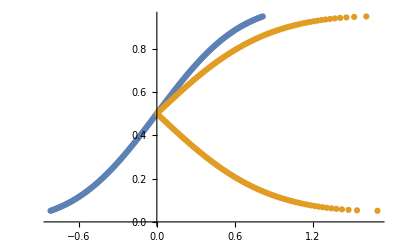

```mathematica
Intersections = ParametricPlot3D[{{X[x],Y[x],Z[0]}, {X[x],Y[x],Z[x]}},{x, x/.Boundaries[[1]], x/.Boundaries[[2]]}, PlotStyle->Directive[Opacity[1]]];
Spheroid = ContourPlot3D[{h[x,y,z]==1},{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.3],Specularity[White,30]], AxesLabel->Automatic, AspectRatio->1];
Show[ Spheroid, Intersections]
ListPlot[{dat, data}]
```

```mathematica
l
```

{1.69449,1.53761,1.4721,1.42148,1.3785,1.34037,1.30567,1.27353,1.24342,1.21495,1.18784,1.16189,1.13692,1.11283,1.08949,1.06682,1.04476,1.02325,1.00222,0.981649,0.961483,0.941692,0.922249,0.903126,0.8843,0.86575,0.847457,0.829406,0.811579,0.793963,0.776545,0.759315,0.742259,0.72537,0.708637,0.692052,0.675608,0.659296,0.64311,0.627043,0.61109,0.595245,0.579502,0.563856,0.548303,0.532838,0.517457,0.502156,0.48693,0.471777,0.456693,0.441675,0.426719,0.411822,0.396982,0.382195,0.367459,0.352771,0.33813,0.323531,0.308974,0.294455,0.279973,0.265525,0.25111,0.236725,0.222369,0.208039,0.193733,0.17945,0.165189,0.150946,0.136721,0.122511,0.108316,0.0941327,0.0799603,0.0657969,0.051641,0.0374909,0.023345,0.00920177,0.00494045,0.0190832,0.0332282,0.0473768,0.0615308,0.0756918,0.0898614,0.104041,0.118233,0.132438,0.146658,0.160895,0.175151,0.189428,0.203726,0.218048,0.232397,0.246773,0.261179,0.275617,0.290088,0.304596,0.319141,0.333727,0.348356,0.363029,0.377751,0.392522,0.407346,0.422226,0.437164,0.452163,0.467227,0.482359,0.497562,0.51284,0.528197,0.543637,0.559163,0.57478,0.590494,0.606308,0.622228,0.63826,0.65441,0.670683,0.687087,0.703629,0.720317,0.737159,0.754163,0.771341,0.788701,0.806256,0.824018,0.842001,0.86022,0.878691,0.897432,0.916464,0.935809,0.955493,0.975543,0.995993,1.01688,1.03824,1.06013,1.08261,1.10574,1.1296,1.15429,1.17993,1.20667,1.23471,1.2643,1.29578,1.32964,1.36663,1.40795,1.45585,1.51551,1.60878}

```mathematica
r
```

```mathematica
Boundaries[[2]]
```

{x→0.816497}

```mathematica
p*x/.Boundaries[[2]]
```

0.816497 p